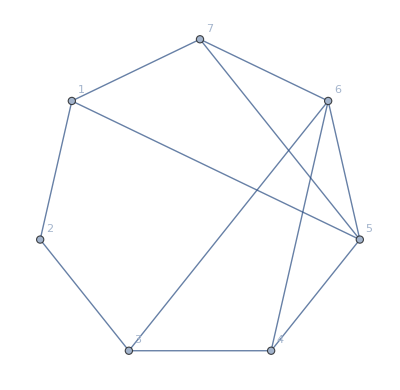
```mathematica
Select[FindFullFormula[-Graphics-],SymbolRank[#]==4&]
```

{v1x26x35x47,v1x247x35x6,v16x2x35x47,v16x27x35x4,v16x25x3x47,v16x25x37x4,v16x247x3x5,v16x24x37x5,v16x24x35x7,v14x27x35x6,v14x26x37x5,v14x26x35x7,v14x25x37x6,v13x26x47x5,v13x25x47x6,v13x247x5x6}

```mathematica
Target[n_]:=If[EvenQ[n],n/2,3n+1]
```

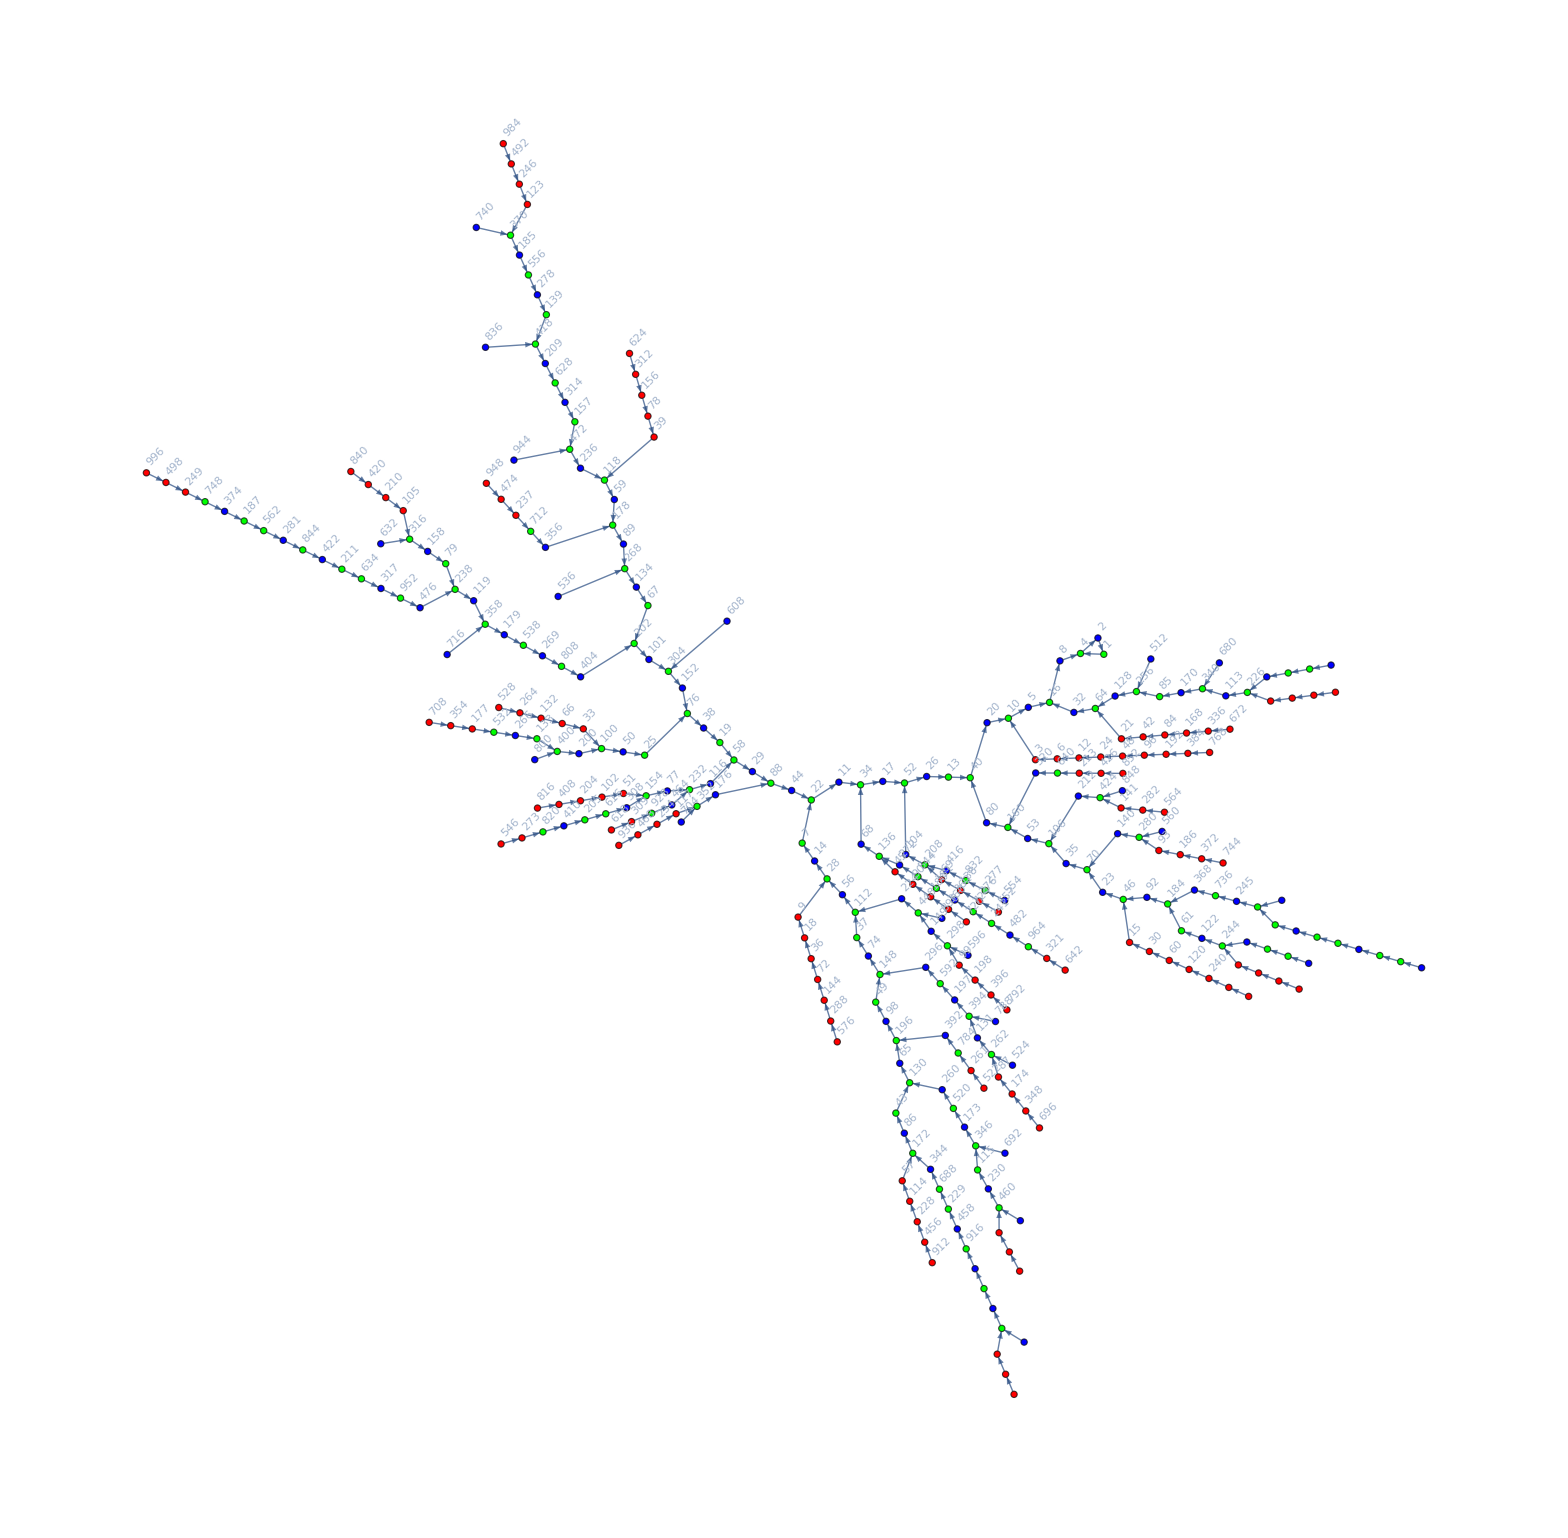

```mathematica
With[
{edges=Table[n->Target[n],{n,1,1000}]},
With[{g=WeaklyConnectedGraphComponents[
Graph[edges,VertexLabels->"Name",
VertexStyle->Map[#->{Red,Green,Blue}[[Mod[#,3]+1]]&,VertexList[Graph[edges]]],
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->600
]
][[1]]}
,
Graph[g,VertexLabels->Map[#->Rotate[#,Pi/4]&,VertexList[g]],
VertexStyle->Map[#->{Red,Green,Blue}[[Mod[#,3]+1]]&,VertexList[g]],
GraphLayout->"RadialEmbedding",
ImageSize->2400]
]
]
```